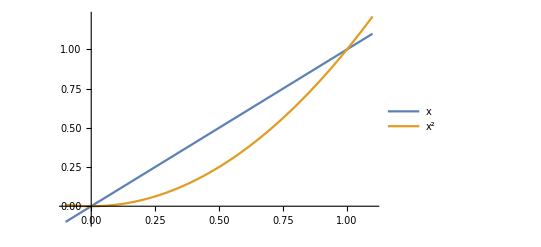

```mathematica
Plot[{x,x^2},{x,-0.1,1.1},PlotLegends->"Expressions"]
```

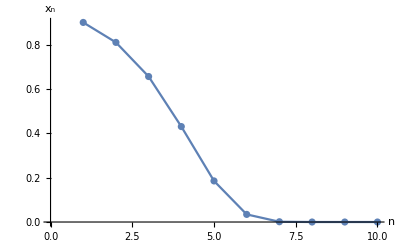

```mathematica
sol1=RecurrenceTable[{x[n+1]==x[n]^2,x[0]==0.9},x,{n,0,9}];
ListPlot[sol1,AxesLabel->{n,Subscript[x,n]},Joined->True,Mesh->All]
```

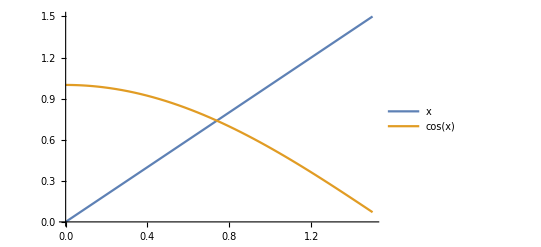

```mathematica
Plot[{x,Cos[x]},{x,0,1.5},PlotLegends->"Expressions"]
```

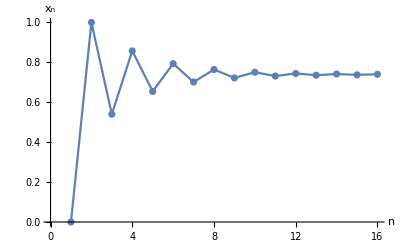

```mathematica
sol2=RecurrenceTable[{x[n+1]==Cos[x[n]],x[0]==0},x,{n,0,15}];
ListPlot[sol2,AxesLabel->{n,Subscript[x,n]},Joined->True,Mesh->All]
```

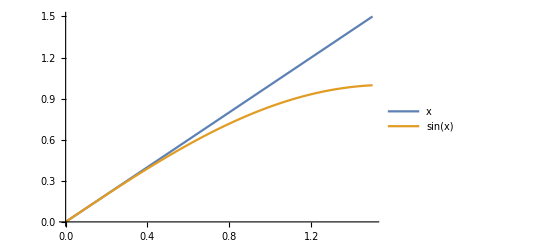

```mathematica
Plot[{x,Sin[x]},{x,0,1.5},PlotLegends->"Expressions"]
```

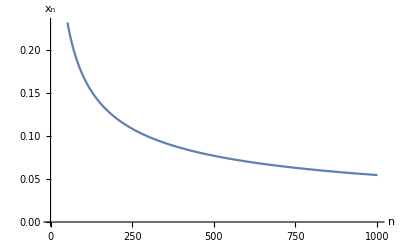

```mathematica
sol3=RecurrenceTable[{x[n+1]==Sin[x[n]],x[0]==1},x,{n,0,1000}];
ListPlot[sol3,AxesLabel->{n,Subscript[x,n]},Joined->True]
```

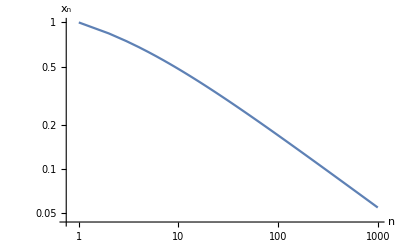

```mathematica
ListPlot[sol3,AxesLabel->{n,Subscript[x,n]},Joined->True,ScalingFunctions->{"Log","Log"},PlotRange->All]
```